```mathematica
Block[
{n=1000,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
While[
True,
s=RandomInteger[{1,n}];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
Print[A];
Print[sum];
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print[A];
Print[sum];
]
```

{444}

2.63454×10^304

{444,774}

2.63454×10^304

{444,774}

2.63454×10^304

```mathematica
Block[
{n=50,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
Print[ListLinePlot[Table[Abs[Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]))],{s,0,n}],PlotRange->All]];
]
```

-Graphics-

```mathematica
Block[
{n=100,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
Print[ListLinePlot[Table[Abs[Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]))],{s,0,n}],PlotRange->All]];
]
```

-Graphics-

```mathematica
Block[
{n=200,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
Print[ListLinePlot[Table[Abs[Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]))],{s,0,n}],PlotRange->All]];
]
```

-Graphics-

```mathematica
Block[
{n=400,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
Print[ListLinePlot[Table[Abs[Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]))],{s,0,n}],PlotRange->All]];
]
```

-Graphics-

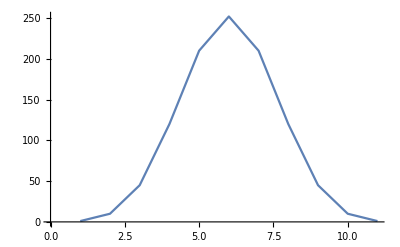

```mathematica
Block[
{n=10},
ListLinePlot[Table[Binomial[n,s],{s,0,n}]]
]
```

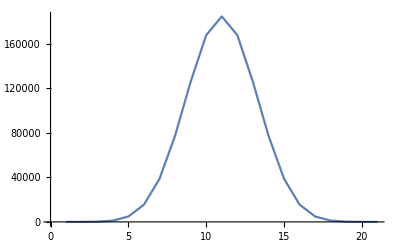

```mathematica
Block[{n=20},ListLinePlot[Table[Binomial[n,s],{s,0,n}]]]
```

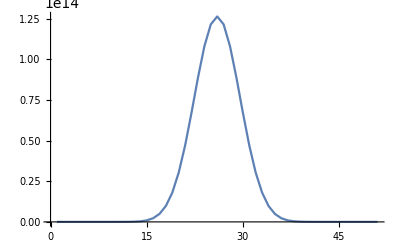

```mathematica
Block[{n=50},ListLinePlot[Table[Binomial[n,s],{s,0,n}]]]
```

```mathematica
Block[{n=100},ListLinePlot[Table[Binomial[n,s],{s,0,n}],PlotStyle->All]]
```

-Graphics-

```mathematica
RandomVariate[BinomialDistribution[10,0.3],10]
```

{4,5,2,2,3,4,0,2,2,3}

```mathematica
PDF[BinomialDistribution[10,0.3],x]
```

Piecewise[{{0.3^x 0.7^(10-x) Binomial[10,x], 0≤x≤10}, {0, True}}]

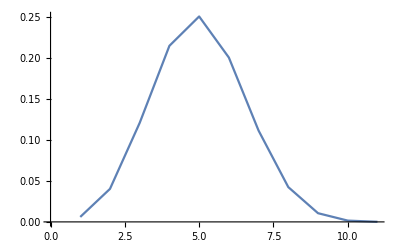

```mathematica
ListLinePlot[Table[PDF[BinomialDistribution[10,1/2.5],x],{x,0,10}]]
```

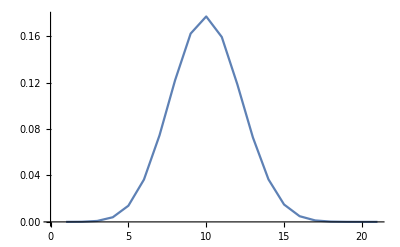

```mathematica
Block[{m=20},ListLinePlot[Table[PDF[BinomialDistribution[m,(m/2-1)/m],x],{x,0,m}]]]
```

```mathematica
Block[
{n=10,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
While[
True,
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Print[s];Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
Print[A];
Print[sum];
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print[A];
Print[Length[A]];
Print[sum];
]
```

{3}

7.17077×10^7

3

{3,6}

2.69756×10^8

{3,6,5}

3.80443×10^8

3

5

{3,6,5,4}

4.16693×10^8

{3,6,5,4,2}

4.50518×10^8

3

6

2

4

{3,6,5,4,2,1}

4.44061×10^8

3

5

4

6

2

5

5

4

1

5

4

4

3

2

4

6

4

5

6

4

5

5

{3,6,5,4,2,1,8}

4.57012×10^8

4

4

6

4

4

3

1

3

5

3

3

3

5

2

5

6

2

3

4

5

5

4

1

4

5

4

6

5

4

3

6

4

5

1

4

3

2

3

5

4

4

6

3

4

6

1

5

5

3

3

2

5

5

5

6

4

4

6

2

3

3

4

3

3

5

4

{3,6,5,4,2,1,8,7}

4.75622×10^8

4

5

5

5

3

2

6

2

3

5

3

5

4

5

4

5

3

8

6

6

5

3

2

6

4

2

{3,6,5,4,2,1,8,7,0}

4.75943×10^8

{3,6,5,4,2,1,8,7,0}

9

4.75943×10^8

```mathematica
Block[
{n=10,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 395

Number of samples -> 9

4.75943×10^8

```mathematica
Block[
{n=50,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 2916

Number of samples -> 25

-3.40114×10^20

```mathematica
Block[
{n=100,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 127

Number of samples -> 23

1.10363×10^36

```mathematica
Block[
{n=100,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 11

Number of samples -> 10

-7.13433×10^35

```mathematica
Block[
{n=100,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 102

Number of samples -> 23

9.90134×10^35

```mathematica
Block[
{n=200,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 202

Number of samples -> 36

2.25132×10^66

```mathematica
Block[
{n=500,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 626

Number of samples -> 60

2.22489×10^156

```mathematica
Block[
{n=1000,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 486

Number of samples -> 73

4.38833×10^307

```mathematica
Block[
{n=2000,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 745

Number of samples -> 106

-1.2508422680146×10^609

```mathematica
Block[
{n=2*10^4,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 162

Number of samples -> 119

-1.52847608844997×10^6028

```mathematica
Block[
{n=2*10^5,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 102

Number of samples -> 95

1.02131918589669×10^60214

```mathematica
Block[
{n=2*10^6,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 25

Number of samples -> 25

1.16793394758303×10^602068

```mathematica
Block[
{n=5*10^6,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 111

Number of samples -> 110

1.17002648191358×10^1505158

```mathematica
Block[
{n=5*10^6,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 63

Number of samples -> 61

1.40403702448966×10^1505158

```mathematica
Block[
{n=2*10^6,r,s,A,k=1.38*10^(-23),T=300,P=7*10^5,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Print["Number of trials -> ",r];
Print["Number of samples -> ",Length[A]];
Print[sum];
]
```

Number of trials -> 43

Number of samples -> 43

8.31260241946401×10^602067

```mathematica
Block[
{MonteCarloSum,n=2*10^4,k=1.38*10^(-23),T=200,P=1000,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
MonteCarloSum[n_,P_,T_,q_,m_,h_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
Print[n k T Log[k T/q/E0]+3n k T/2 Log[2 π m k T/h^2]+k T Log[MonteCarloSum[n,P,T,q,m,h,E0]]];
]
```

1.83439×10^-15

```mathematica
Block[
{MonteCarloSum,n=2*10^4,k=1.38*10^(-23),T=400,P=1000,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
MonteCarloSum[n_,P_,T_,q_,m_,h_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
Print[n k T Log[k T/q/E0]+3n k T/2 Log[2 π m k T/h^2]+k T Log[MonteCarloSum[n,P,T,q,m,h,E0]]];
]
```

3.86008×10^-15

```mathematica
Block[
{MonteCarloSum,n=2*10^4,k=1.38*10^(-23),T=400,P=1000,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
MonteCarloSum[n_,P_,T_,q_,m_,h_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
Print[n  Log[k T/q/E0]+3n /2 Log[2 π m k T/h^2]+Log[MonteCarloSum[n,P,T,q,m,h,E0]]];
]
```

699290.

```mathematica
Block[
{MonteCarloSum,n=2*10^4,k=1.38*10^(-23),T=400,P=10^6,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
MonteCarloSum[n_,P_,T_,q_,m_,h_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
Print[n k T Log[k T/q/E0]+3n k T/2 Log[2 π m k T/h^2]+k T Log[Abs[MonteCarloSum[n,P,T,q,m,h,E0]]]];
]
```

3.86007×10^-15

```mathematica
Block[
{MonteCarloSum,n=2*10^4,k=1.38*10^(-23),T=400,P=10^9,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
MonteCarloSum[n_,P_,T_,q_,m_,h_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
Print[n Log[k T/q/E0]+3n/2 Log[2 π m k T/h^2]+ Log[Abs[MonteCarloSum[n,P,T,q,m,h,E0]]]];
]
```

699286.

```mathematica
Block[
{MonteCarloSum,n=2*10^4,k=1.38*10^(-23),T=400,P=10^6,q=1.6*10^(-19),m=10^(-26),h=6.63*10^(-34),E0=10^15},
MonteCarloSum[n_,P_,T_,q_,m_,h_,E0_]:=Block[
{r,s,A,sum,sum1},
sum=0;
A={};
r=0;
While[
True,
r=r+1;
s=RandomVariate[BinomialDistribution[n,(n/2-1)/n]];
If[MemberQ[A,s],Continue[],AppendTo[A,s]];
sum1=sum;
sum=sum+Binomial[n,s]*(-1)^s(HypergeometricPFQ[{1},{1/3,2/3},-(q E0)^3 (n+s)^3/216/(k T)^2/P]+π/18 Sqrt[k T/P](q E0(n+s)/k/T)^(3/2)(BesselJ[1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]-BesselJ[-1/3,Sqrt[k T/54/P](q E0(n+s)/k/T)^(3/2)]));
If[Abs[sum1-sum]/Abs[sum1+0.01]<10^(-3),Break[]];
];
Return[sum];
];
Plot3D[n Log[k T/q/E0]+3n /2 Log[2 π m k T/h^2]+Log[Abs[MonteCarloSum[n,P,T,q,m,h,E0]]],{T,200,1500},{P,10^5,10^8}]//Print;
]
```

$Aborted